```mathematica
SetDirectory["/Users/sinbi/desktop/STUDY/Data_get/hh"];
Needs["ErrorBarPlots`"];
Get["/Users/sinbi/desktop/STUDY/Data_get/ErrorBarLogPlots.m"];
Get["/Users/sinbi/desktop/STUDY/Data_get/ProtonFluxELDRAnn.m"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

## AMS02-Experiment Error Bar Import

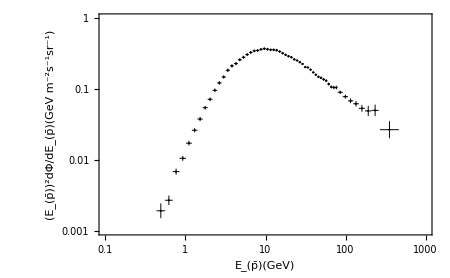

```mathematica
IErrorh= Import["/Users/sinbi/desktop/study/Data_get/Error_data_AMS02_Full.dat","Table",HeaderLines-> 1];
Length[IErrorh];
IErrorh1=Table[{IErrorh[[i,1]],IErrorh[[i,2]],(IErrorh[[i,4]]-IErrorh[[i,3]])/2,(IErrorh[[i,6]]-IErrorh[[i,5]])/2},{i,1,Length[IErrorh]}];
IErrorh2=IErrorh1/.{x_,y_,z_,k_}->{{x,y},ErrorBar[z,k]};
ErroPloth=ErrorListLogLogPlot[IErrorh2,Frame->True,Axes->False,PlotRange->{{10^-1,10^3},{10^-3,1}}, ErrorBarFunction->Automatic,ImageSize->450,PlotStyle->{Black,AbsolutePointSize[1.5],AbsoluteThickness[0.7]},FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

## Get Background(BG)

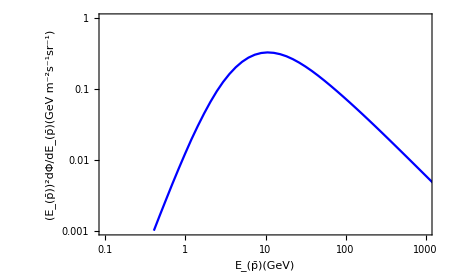

```mathematica
BGh=Import["/Users/sinbi/desktop/study/Data_get/AMSMD.dat","Table","HearderLines"->1];
Length[BGh];
ifBGh=Interpolation[BGh];
BGPloth=ListLogLogPlot[ifBGh,Joined->True,Axes->False,Frame->True,PlotRange->{{10^-1,10^3},{10^-3,1}},ImageSize->450,PlotStyle->{Blue},FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

## Dark Matter(DM)

```mathematica
primaryh="h";
haloh="Ein";
propagationh="MAX";
mDMh=300;
σvh=0.7*10^-26;
Eγ=10^lEγ;
```

```mathematica
ifPoh=Interpolation[Table[{10^lEγ,10^lEγ 10.^ ProtonFluxELDRAnn[primaryh, haloh, propagationh][mDMh, σvh,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}]];
```

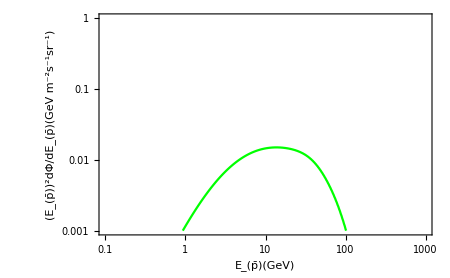

```mathematica
PlotMEDh=ListLogLogPlot[ifPoh,PlotRange->{{10^-1,10^3},{10^-3,1}},Joined->True,PlotStyle->Green,Frame->True,Axes->False,ImageSize->450,FrameTicks-> Automatic, FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

## SUM=BG+DM

InterpolatingFunction[…]

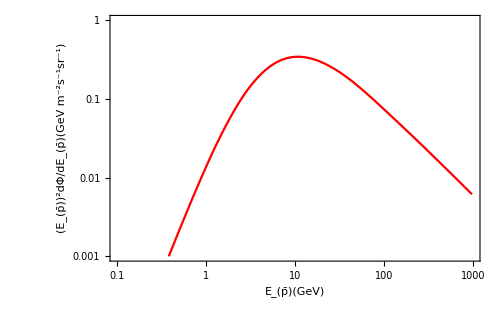

```mathematica
Sumdatah=Interpolation[Table[{x,ifBGh[x]+ifPoh[x]},{x,0.18,10^2.99,0.1}]]
SumPloth=ListLogLogPlot[Sumdatah,Joined->True,PlotRange->{{10^-1,10^3},{10^-3,1}},PlotStyle->Red,Frame->True,Axes->False,ImageSize->500 ,FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

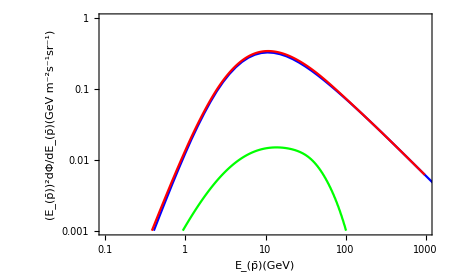

```mathematica
Show[BGPloth,PlotMEDh,SumPloth]
```

## χ^2- Fitting

```mathematica
SumYh=Table[Sumdatah[IErrorh1[[i,1]]],{i,Length[IErrorh]}];
IErrorYh=Flatten[Table[{IErrorh1[[i,2]]},{i,1,Length[IErrorh]}],1];
IErrorSizeh=Flatten[Table[{IErrorh1[[i,4]]},{i,1,Length[IErrorh]}],1];chiSUMh=((SumYh-IErrorYh)/IErrorSizeh)^2;
Sumh1=Sum[chiSUMh[[i]],{i,1,Length[IErrorh]}]
Re[Sumh1]
```

102.471

102.471

## Mass-σv graph

```mathematica
ClearAll[σv02]
```

```mathematica
mDM02=10^lmDM02;
```

```mathematica
σv02=10^lσv02;
```

```mathematica
ifPoh2=Interpolation[Table[{10^lEγ,10^lEγ 10.^ ProtonFluxELDRAnn[primaryh, haloh, propagationh][mDM02, σv02,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}]];
```

```mathematica
Sumdatah2=Interpolation[Table[{x,ifBGh[x]+ifPoh2[x]},{x,0.18,10^2.99,0.1}]];
SumYh2=Table[Sumdatah2[IErrorh1[[i,1]]],{i,Length[IErrorh]}];
chiSUMh2=((SumYh2-IErrorYh)/IErrorSizeh)^2;
FinalSumh=Sum[chiSUMh2[[i]],{i,1,Length[IErrorh]}];
```

```mathematica
conth=Flatten[Table[Re[{mDM02,lσv02,σv02,FinalSumh}],{lmDM02,2.12,2.55,0.01},{lσv02,-27.0,-25.0,0.05}], 1];
Export["hh_EIN_MAX.dat",conth,"Table"];
```

```mathematica
contableh=Import["/Users/sinbi/desktop/study/Data_get/hh/hh_EIN_MAX.dat","Table",HeaderLines->1]
```

{{131.826,-26.95,1.12202×10^-27,109.588},{131.826,-26.9,1.25893×10^-27,107.197},{131.826,-26.85,1.41254×10^-27,105.202},1797,{354.813,-25.1,7.94328×10^-26,4743.72},{354.813,-25.05,8.91251×10^-26,6062.94},{354.813,-25.,1.×10^-25,7739.59}}
 |  |  |  |

```mathematica
conthLog=Table[{contableh[[i,1]],contableh[[i,2]], contableh[[i, 4]]},{i, Length[contableh]}];
```

```mathematica
Export["hh_table_EIN_MAX.dat",conthLog,"Table"]
```

hh_table_EIN_MAX.dat

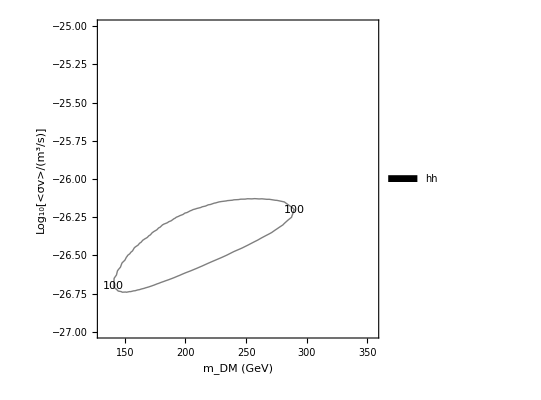

```mathematica
ListContourPlot[conthLog,Contours-> {65, 70,80,100},
FrameLabel->{"m_DM (GeV)","Log_10[<σv>/(m^3/s)]"}, ContourLabels->All,ContourShading->None,PlotLegends->Placed[SwatchLegend[{"hh"},LegendMarkerSize->20],Right]]
```

```mathematica
spdp
```

spdp